# Meshing The Drums

Some folks had some problems with the drum meshes.  I think there were different bits of problems for the FENICS and GRIDAP folks.  As I understand it the “boundary tags” were not working for the some of the GridApp folks and the FENICS folks currently need to “fake” the boundary with an equation.

The two may need different solutions but lets think about what would be the easiest way to do things.

## The circle is easy!

Defined entirely by the radius R

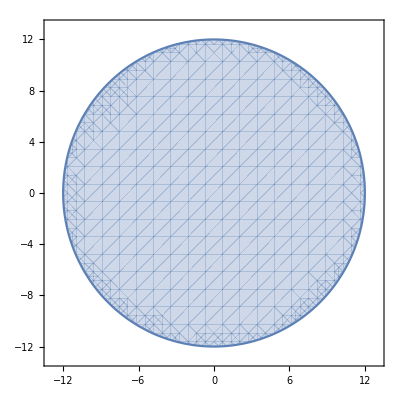

```mathematica
R=12;
RegionPlot[ x^2+y^2≤R^2,{x, -13,13},{y,-13,13}]
```

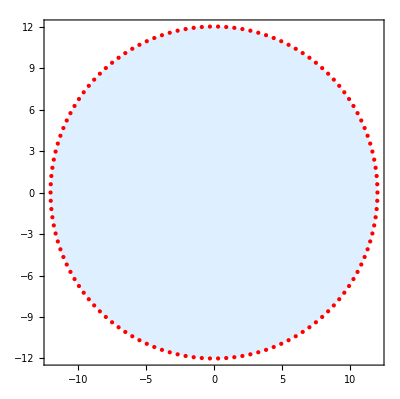

```mathematica
R=12.0; n=126;
BorderPoints=Table[R{Cos[θ],Sin[θ]},{θ,2π/n, 2π, 2π/n}];
Graphics[{{LightBlue,Polygon[BorderPoints]},{Red, Point[BorderPoints]}},Frame->True]
```

## The Square and Rectangle Can be done together!

Defined by the two side lengths 2a and 2b along with the rounded of radius r.  The center of each rounding off circle is displaced {r,r} towards the inside of the rectangle from the corner.

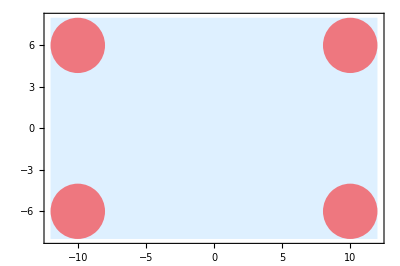

```mathematica
{a,b,r}={12.0,8.0,2.0};
Graphics[{
{LightBlue,Rectangle[{-a,-b},{a,b}]},
{Opacity[0.5], Red,
Disk[{a-r,b-r},r],
Disk[{-a+r,b-r},r],
Disk[{-a+r,-b+r},r],
Disk[{a-r,-b+r},r]}},Frame->True]
```

We can make the rounded off rectangle we want by putting edges together.  All I really need are dots around the outside of each quarter circle in the correct ccw order!  Lets think about it for a second.

{a,b}  we need 0≤θ≤π/2.

{-a,b}  we need π/2≤θ≤π.

{-a,-b}  we need π≤θ≤3π/2.

{a,-b}  we need 3π/2≤θ≤2π.

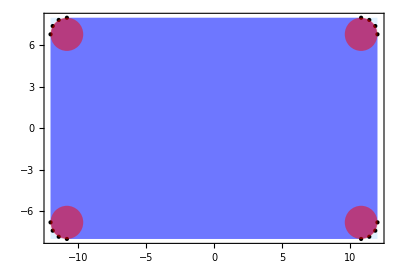

```mathematica
n=6;
BorderPoints=Join[
Table[{a-r,b-r}+r {Cos[θ],Sin[θ]},{θ,0,π/2,π/n}],
Table[{-a+r,b-r}+r {Cos[θ],Sin[θ]},{θ,π/2,π,π/n}],
Table[{-a+r,-b+r}+r {Cos[θ],Sin[θ]},{θ,π,3π/2,π/n}],
Table[{a-r,-b+r}+r {Cos[θ],Sin[θ]},{θ,3π/2,2π,π/n}]];
Graphics[{
{LightBlue,Rectangle[{-a,-b},{a,b}]},
{Opacity[0.5],Blue,Polygon[BorderPoints]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,
Disk[{a-r,b-r},r],
Disk[{-a+r,b-r},r],
Disk[{-a+r,-b+r},r],
Disk[{a-r,-b+r},r]}},Frame->True]
```

## Triangles!

We can probably do triangles the same way by rounding of the edges using some trig.  I need three points (counter clock wise) to define a triangle and a rounding radius r.  I can easily compute the center of the triangle.

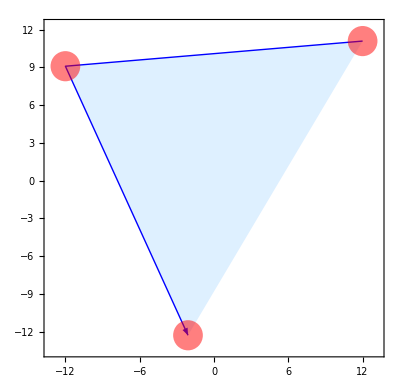

```mathematica
{p1,p2,p3}={{12.0,11.1},{-12.0,9.1},{-2.1,-12.3}};
r=1.2;
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3}]},
{Opacity[0.5], Red,Disk[p1,r],Disk[p2,r],Disk[p3,r]}
},Frame->True]
```

I need to move each circle in along the line bisecting each angle until it is just inside the triangle.  At that point the circle is tangent to both edges!  I am going to add guide lines in the middle of each angle!  The easiest way to compute the bisectors is to compute the “incenter” of the triangle

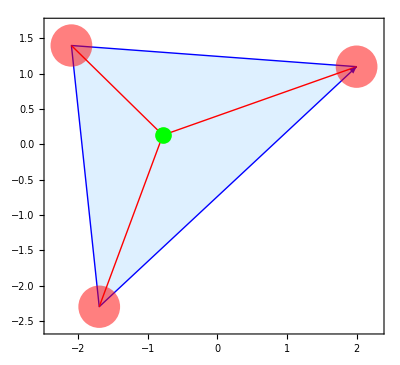

```mathematica
{p1,p2,p3}={{2.0,1.1},{-2.1,1.4},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,pCenter}],Arrow[{p2,pCenter}],Arrow[{p3,pCenter}] },
{PointSize[0.03],Green,Point[pCenter]},
{Opacity[0.5], Red,Disk[p1,r],Disk[p2,r],Disk[p3,r]}
},Frame->True]
```

Now we are going to do some simple trig (on the board) to work out how far to move each disk in!  We will check we did it correctly by computing the correct values of the shifts on the pic below.

{{1.34082,0.494264},{1.37266,0.528468},{1.3988,0.567203},{1.41862,0.609527},{1.43161,0.654415},{1.43748,0.700777},{1.43608,0.747488},{1.42744,0.793414},{1.41178,0.837442},{1.38946,0.878503},{1.36104,0.9156},{1.32721,0.947833},{1.28878,0.974421},{1.24668,0.994717},{1.20195,1.00823},{1.15566,1.01463},{1.10893,1.01377},{-0.876946,0.821586},{-0.900775,0.818311},{-0.924264,0.813138},{-0.947264,0.8061},{-0.969626,0.797242},{-0.991206,0.786621},{-1.01187,0.774305},{-1.03147,0.760374},{-1.0499,0.744917},{-1.06703,0.728033},{-1.08276,0.709831},{-1.09697,0.690428},{-1.10958,0.669949},{-1.12052,0.648525},{-1.1297,0.626294},{-1.13707,0.603399},{-1.14258,0.579987},{-1.52695,-1.40589},{-1.53223,-1.45252},{-1.53018,-1.4994},{-1.52085,-1.54538},{-1.50446,-1.58935},{-1.48142,-1.63022},{-1.45228,-1.667},{-1.41776,-1.69879},{-1.37871,-1.72481},{-1.33608,-1.74442},{-1.29091,-1.75714},{-1.24432,-1.76266},{-1.19743,-1.76085},{-1.1514,-1.75175},{-1.10734,-1.73558},{-1.06635,-1.71275},{-1.02943,-1.6838}}

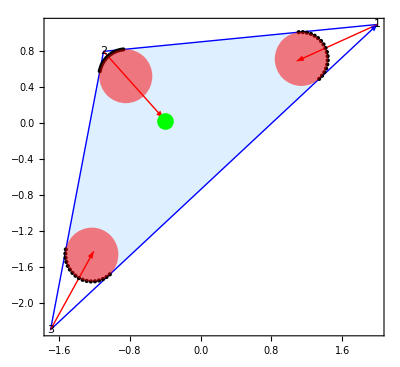

```mathematica
{p1,p2,p3}={{2.0,1.1},{-1.1,0.8},{-1.7,-2.3}};
r=0.3;
{a1,a2,a3}=Map[Norm,{p2-p3,p1-p3,p1-p2}];
pCenter=(a1 p1+a2 p2+a3 p3)/(a1+a2+a3);
(* make unit vectors towards in center *)
{τ1,τ2,τ3}= Map[Normalize,{pCenter-p1,pCenter-p2,pCenter-p3}];
(* make unit vectors pependicular to the τs *)
{n1,n2,n3}=Map[{-#⟦2⟧,#⟦1⟧}&,{τ1,τ2,τ3}];
{θ1,θ2,θ3}= {
0.5 ArcCos[((p2-p1).(p3-p1))/(Norm[p2-p1] Norm[p3-p1])],
0.5 ArcCos[((p3-p2).(p1-p2))/(Norm[p3-p2] Norm[p1-p2])],
0.5 ArcCos[((p2-p3).(p1-p3))/(Norm[p2-p3] Norm[p1-p3])]};

{d1,d2,d3}={r/Sin[θ1],r/Sin[θ2],r/Sin[θ3]};
(* Compute Complementary Angles *)
{θc1,θc2,θc3}={π/2-θ1,π/2-θ2,π/2-θ3};
(* Build Border Points *)
m=8;
BorderPoints=Join[
Table[ p1+τ1 d1 - r (τ1 Cos[θ]+n1 Sin[θ]),{θ,-θc1,θc1,θc1/m}],
Table[ p2+τ2 d2 - r (τ2 Cos[θ]+n2 Sin[θ]),{θ,-θc2,θc2,θc2/m}],
Table[ p3+τ3 d3 - r (τ3 Cos[θ]+n3 Sin[θ]),{θ,-θc3,θc3,θc3/m}]
]
(* Check that it works *)
Graphics[{
{LightBlue,Polygon[{p1,p2,p3}]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,p1+τ1}],Arrow[{p2,p2+τ2}],Arrow[{p3,p3+τ3}] },
{PointSize[0.03],Green,Point[pCenter]},
{Black,Text["1",p1],Text["2",p2],Text["3",p3]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,Disk[p1+d1 τ1,r],Disk[p2+d2 τ2,r],Disk[p3+d3 τ3,r]}
},Frame->True];
Graphics[{
{LightBlue,Polygon[BorderPoints]},
{Blue, Arrow[{p1,p2,p3,p1}]},
{Red,Arrow[{p1,p1+τ1}],Arrow[{p2,p2+τ2}],Arrow[{p3,p3+τ3}] },
{PointSize[0.03],Green,Point[pCenter]},
{Black,Text["1",p1],Text["2",p2],Text["3",p3]},
{Black, Point[BorderPoints]},
{Opacity[0.5], Red,Disk[p1+d1 τ1,r],Disk[p2+d2 τ2,r],Disk[p3+d3 τ3,r]}
},Frame->True]
```

## Semi Circle!

The semi circle is actually a slice off the top of a circle with the corners rounded off. 

It is defined by a big radius “R” a distance “d” up from the diameter and a rounding radius “r”.  It is easier (unless you love trig) to work out how far the disks need to move in now.

If we make up a recipe (or a thing to solve) we can work out what is “just-right”.

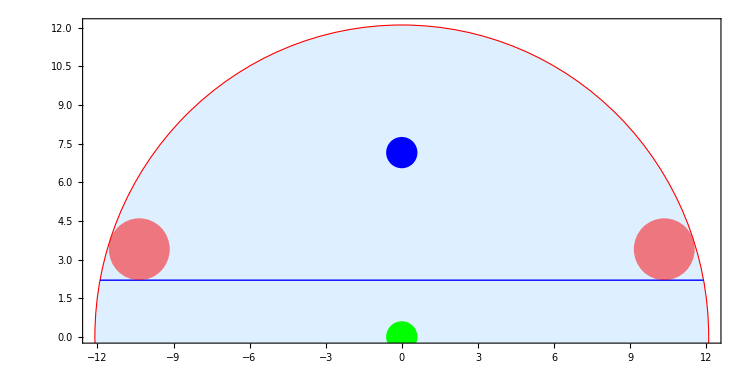

```mathematica
{R,d,r}={12.1,2.2,1.2};
x1=√(R^2-d^2);
s1=1.55;
Graphics[{
{LightBlue,EdgeForm[Red],Disk[{0,0},R]},
{Blue, Line[{{-x1,d},{x1,d}}]},
{PointSize[0.03],Green,Point[{0,0}]},
{PointSize[0.03],Blue,Point[{0,(R+d)/2}]},
{Opacity[0.5], Red,Disk[{-x1+s1,d+r},r],Disk[{x1-s1,d+r},r]}
},Frame->True,
PlotRange->{All,{0,R}}]
```

I need to find the value of the shift s when the big circle
	x^2+y^2=R^2
and the little circle radius r centered at {x1-s,d+r} 
	(x-(x1-s))^2+(y-(d+r))^2=r^2
are tangent. There are three unknowns x,y,and s: all the other things are inputs!  If I write
	f1[x,y]=x^2+y^2 and f2[x,y]=(x-(x1-s))^2+(y-(d+r))^2 
then the tangent condition (think back to Calcus III and Lagrange Multipliers) is
	∇f1[x,y]=λ∇f2[x,y] 
This is one vector equation with one more unknown λ. Writing this out as two scalar equations we have
	2x | = |  2λ(x-(x1-s))
2y | = | 2λ(y-(d+r))   
Putting this all together I have four scalar equations in the four unknowns x, y, s, and λ.  I should be able to get the computer to solve these.

```mathematica
Clear[R,r,x1,d,s,x,y]
x1=√(R^2-d^2);
FullSimplify[
s/.Solve[{
x^2+y^2==R^2,
(x-(x1-s))^2+(y-(d+r))^2==r^2,
2x == 2 λ (x-(x1-s)),
2y == 2 λ (y-(d+r))
},
{s,x,y,λ}
]
]
```

Solve::nongen: Solutions may not be valid for all values of parameters.

{((r-R) √(d+2 r-R) √(d+R))/(√(-(r-R)^2))+√(-d^2+R^2),(√(-(r-R)^2) √(d+2 r-R) √(d+R))/(r-R)+√(-d^2+R^2),(√(d-R) √(-(r+R)^2) √(d+2 r+R))/(r+R)+√(-d^2+R^2),(√(d-R) (r+R) √(d+2 r+R))/(√(-(r+R)^2))+√(-d^2+R^2)}

I know that d<R, r<R, and I need 0<s<R.  I am going to work out which is the appropriate solution.

```mathematica
TestsFuns[R_,r_,d_]:={((r-R) √(d+2 r-R) √(d+R))/(√(-(r-R)^2))+√(-d^2+R^2),(√(-(r-R)^2) √(d+2 r-R) √(d+R))/(r-R)+√(-d^2+R^2),(√(d-R) √(-(r+R)^2) √(d+2 r+R))/(r+R)+√(-d^2+R^2),(√(d-R) (r+R) √(d+2 r+R))/(√(-(r+R)^2))+√(-d^2+R^2)}
```

It looks as though the correct answer is the first one.

```mathematica
Chop[TestsFuns[12,1,0.2]]
```

{1.06398,22.9327,-0.946164,24.9428}

I just realised I need all the bits

```mathematica
sHalfCircle[R_,r_,d_]:=((r-R) √(d+2 r-R) √(d+R))/(√(-(r-R)^2))+√(-d^2+R^2)
```

Lets check!  I think it looks good.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→5.64267-1.50152 ⅈ,y→1.85253+4.57352 ⅈ},{x→5.64267+1.50152 ⅈ,y→1.85253-4.57352 ⅈ}}

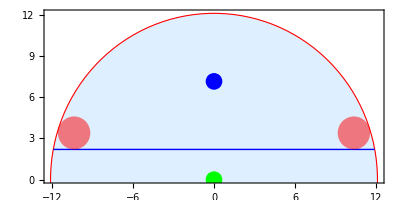

```mathematica
{R,d,r}={12.1,2.2,1.2};
x1=√(R^2-d^2);
s=sHalfCircle[R,r,d];
Solve[{x^2+y^2==R, (x-(x1-s))^2+(y-(d+r))^2==r^2},{x,y}]
Graphics[{
{LightBlue,EdgeForm[Red],Disk[{0,0},R]},
{Blue, Line[{{-x1,d},{x1,d}}]},
{PointSize[0.03],Green,Point[{0,0}]},
{PointSize[0.03],Blue,Point[{0,(R+d)/2}]},
{Opacity[0.5], Red,Disk[{-x1+s,d+r},r],Disk[{x1-s,d+r},r]}
},Frame->True,
PlotRange->{All,{0,R}}]
```

All I have to do now is make the dots for the polygons.  To make boundary dots I need to know the intersection points.

I am going to redo this purely numerically because it will be easier

{{1.54216,11.4963,3.77431}}

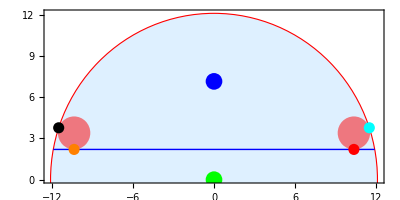

```mathematica
Clear[s,x,y]
{R,d,r}={12.1,2.2,1.2};
x1=√(R^2-d^2);
{{sSol,xSol,ySol}}=Select[
{s,x,y}/.NSolve[{
x^2+y^2==R^2,
(x-(x1-s))^2+(y-(d+r))^2==r^2,
2x == 2 λ (x-(x1-s)),
2y == 2 λ (y-(d+r))
},
{s,x,y,λ}
],
And[0<#⟦1⟧<R]&]
Graphics[{
{LightBlue,EdgeForm[Red],Disk[{0,0},R]},
{Blue, Line[{{-x1,d},{x1,d}}]},
{PointSize[0.03],Green,Point[{0,0}]},
{PointSize[0.03],Blue,Point[{0,(R+d)/2}]},
{Opacity[0.5], Red,Disk[{-x1+sSol,d+r},r],Disk[{x1-sSol,d+r},r]},
{PointSize[0.02],Black,Point[{-xSol,ySol}],Red,Point[{x1-sSol,d}]},,
{PointSize[0.02],Cyan,Point[{xSol,ySol}],Orange,Point[{-x1+sSol,d}]},
},Frame->True,
PlotRange->{All,{0,R}}]
```

Finally the #$#@$ points

{{1.54216,11.4963,3.77431}}

0.31722

{{11.4963,3.77431},{7.40911×10^-16,12.1},{-11.4963,3.77431},{10.3562,2.2},{11.3281,2.69614},{11.4963,3.77431}}

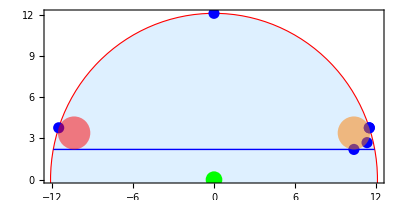

```mathematica
Clear[s,x,y]
{R,d,r}={12.1,2.2,1.2};
x1=√(R^2-d^2);
{{sSol,xSol,ySol}}=Select[
{s,x,y}/.NSolve[{
x^2+y^2==R^2,
(x-(x1-s))^2+(y-(d+r))^2==r^2,
2x == 2 λ (x-(x1-s)),
2y == 2 λ (y-(d+r))
},
{s,x,y,λ}
],
And[0<#⟦1⟧<R]&]
{nBig,nSmall}={2,2};
θBig=ArcTan[xSol,ySol]
θSmall=ArcTan[xSol-(x1-sSol),ySol-(d+r)];
BorderPoints=Join[
Table[ R{Cos[θ],Sin[θ]},{θ,θBig,π-θBig, (π-2θBig)/nBig}],
Table[ {x1-sSol,d+r}+r{Cos[θ],Sin[θ]},{θ,-π/2,θSmall, (π/2+θSmall)/nSmall}]
]
Hmm=Graphics[{
{LightBlue,EdgeForm[Red],Disk[{0,0},R]},
{Blue, Line[{{-x1,d},{x1,d}}]},
{PointSize[0.03],Green,Point[{0,0}]},
{PointSize[0.02],Blue,Point[BorderPoints]},
{Opacity[0.5], Red,Disk[{-x1+sSol,d+r},r],Orange,Disk[{x1-sSol,d+r},r]}
},Frame->True,
PlotRange->{All,{0,R}}]
```

```mathematica
?ArcTan
```